```mathematica
MatrixExp[r*PauliMatrix[1]]//FullSimplify
```

{{Cosh[r],Sinh[r]},{Sinh[r],Cosh[r]}}

```mathematica
U = MatrixExp[{{0,u},{0,0}}]
```

{{1,u},{0,1}}

```mathematica
T= MatrixExp[t*PauliMatrix[3]]
```

{{ⅇ^t,0},{0,ⅇ^-t}}

```mathematica
V = MatrixExp[{{0,0},{-v,0}}]
```

{{1,0},{-v,1}}

```mathematica
U.T.V//FullSimplify
```

{{ⅇ^t-ⅇ^-t u v,ⅇ^-t u},{-ⅇ^-t v,ⅇ^-t}}

```mathematica
Solve[E^t-E^(-t)*uv==E^(-t),uv]
```

{{uv→-1+ⅇ^(2 t)}}

```mathematica
Sqrt[1-E^(2*t)]
```

√(1-ⅇ^(2 t))

```mathematica
E^t+E^(-t)*(1-E^(2t))//FullSimplify
```

ⅇ^-t

```mathematica
TrigToExp[Cosh[r]]
```

ⅇ^-r/2+ⅇ^r/2

```mathematica
Cosh[r]/Sinh[r]
```

Coth[r]

```mathematica
Log[Cosh[r]]//FullSimplify
```

Log[Cosh[r]]

```mathematica
Integrate[E^(2*I*w*t),{t,0,T}]//FullSimplify
```

-(ⅈ (-1+ⅇ^(2 ⅈ T w)))/(2 w)

```mathematica
DSolve[{a'[t]==-I*w*a[t]+2*L*ad[t], ad'[t]==I*w*ad[t]+2*L*a[t]},{a[t], ad[t]},t]//FullSimplify
```

{{a[t]→C[1] Cosh[t √(4 L^2-w^2)]+((-ⅈ w C[1]+2 L C[2]) Sinh[t √(4 L^2-w^2)])/(√(4 L^2-w^2)),ad[t]→C[2] Cosh[t √(4 L^2-w^2)]+((2 L C[1]+ⅈ w C[2]) Sinh[t √(4 L^2-w^2)])/(√(4 L^2-w^2))}}

```mathematica
Integrate[R*(R*x)^2/Sqrt[Pi]*Exp[-(R*x)^2/2]^2,{x,-Infinity,Infinity}]-Integrate[R*(R*x)/Sqrt[Pi]*Exp[-(R*x)^2/2]^2,{x,-Infinity,Infinity}]^2
```

ConditionalExpression[R^3/(2 (R^2)^(3/2)), Re[R^2]>0]

```mathematica
Integrate[1/Sqrt[Pi]*Exp[-(R*x)^2/2]^2,{x,-Infinity,Infinity}]
```

ConditionalExpression[1/(√(R^2)), Re[R^2]>0]

```mathematica
a[t]=b[t]*Exp[-I*w*t];
```

```mathematica
D[a[t],t]+I*w*a[t]
```

ⅇ^(-ⅈ t w) b'[t]

```mathematica
b[t] = c1*Exp[2*L*t]+c2*Exp[-2*L*t]
```

c2 ⅇ^(-2 L t)+c1 ⅇ^(2 L t)

```mathematica
D[b[t],{t,2}]-4*L^2*b[t]//FullSimplify
```

0

```mathematica
b[t]=(a1+I*b1)*Cosh[2*L*t]+(a2+I*b2)*Sinh[2*L*t];
```

```mathematica
bd[t]=Conjugate[b[t]]
```

Conjugate[(a1+ⅈ b1) Cosh[2 L t]+(a2+ⅈ b2) Sinh[2 L t]]

```mathematica
ExpToTrig[E^(4*L*t)+E^(-4*L*t)]/4
```

1/2 Cosh[4 L t]

```mathematica
Cosh[0]
```

1

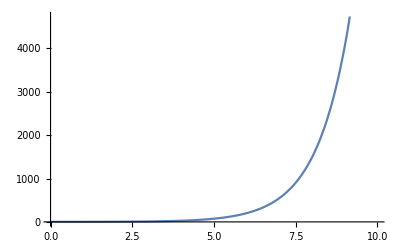

```mathematica
Plot[Cosh[t],{t,0,10}]
```

```mathematica
DeclareNonCommutative[a,A]
```

DeclareNonCommutative[a,A]

```mathematica
(*Q1*)
```

```mathematica
Q1[Rz_,Iz_,r_]:=(Exp[-(Rz^2+Iz^2)]/Cosh[r])*Abs[Sum[(Rz-I*Iz)^(2n)*(Tanh[r])^n/(2^n*Factorial[n]),{n,0,100}]]^2
```

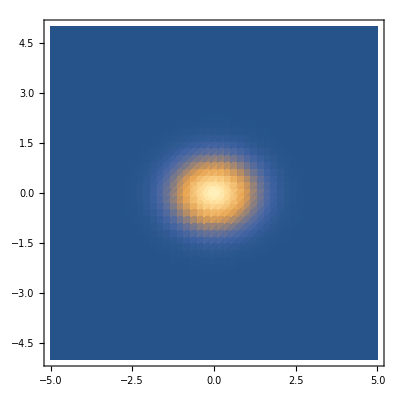

```mathematica
DensityPlot[Q1[Rz,Iz,0.2],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```

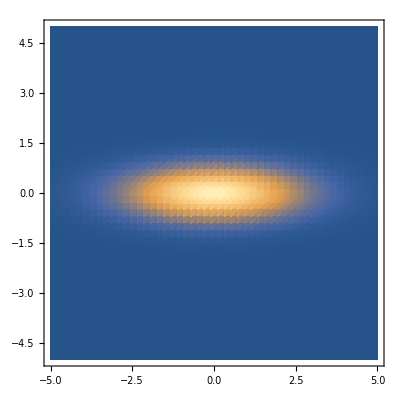

```mathematica
DensityPlot[Q1[Rz,Iz,1.2],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```

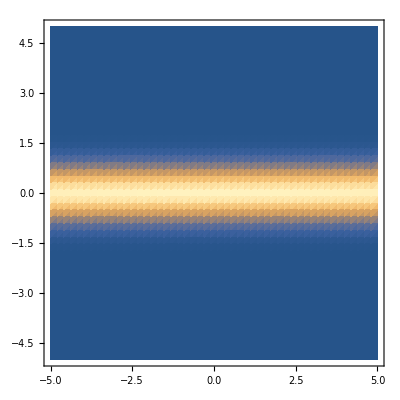

```mathematica
DensityPlot[Q1[Rz,Iz,4],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```

```mathematica
(*Q2*)
```

```mathematica
Q2[Rz_,Iz_,r_]:=(Exp[-((Rz-2)^2+Iz^2)]/Cosh[r])*Abs[Sum[(Rz-I*Iz - 2)^(2n)*(Tanh[r])^n/(2^n*Factorial[n]),{n,0,100}]]^2
```

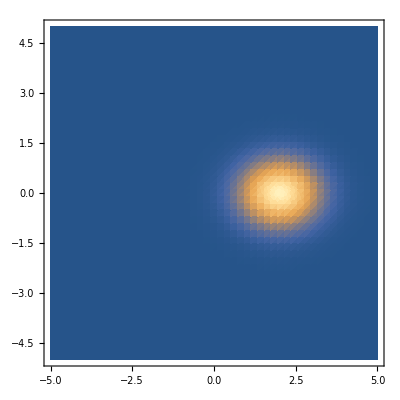

```mathematica
DensityPlot[Q2[Rz,Iz,0.2],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```

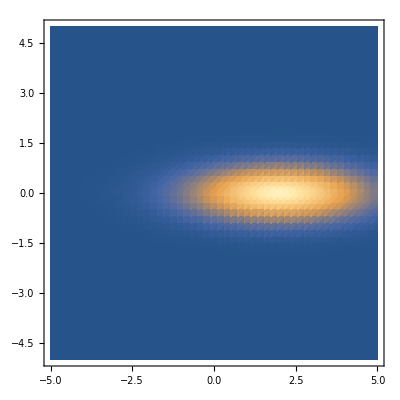

```mathematica
DensityPlot[Q2[Rz,Iz,1.2],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```

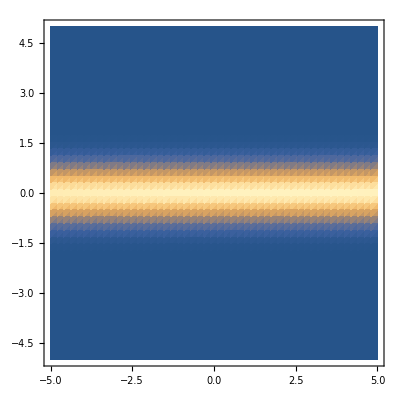

```mathematica
DensityPlot[Q2[Rz,Iz,4],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```

```mathematica
(*Q3*)
```

```mathematica
Q3[Rz_,Iz_,r_]:=(Exp[-((Rz-2*Cosh[r]+2*Sinh[r])^2+Iz^2)]/Cosh[r])*Abs[Sum[(Rz-I*Iz - 2*Cosh[r]+2*Sinh[r])^(2n)*(Tanh[r])^n/(2^n*Factorial[n]),{n,0,100}]]^2
```

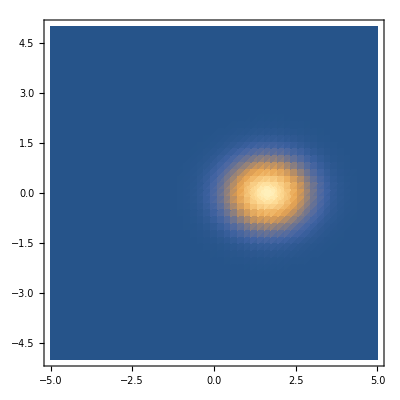

```mathematica
DensityPlot[Q3[Rz,Iz,0.2],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```

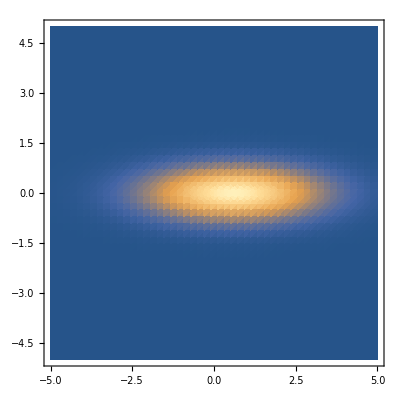

```mathematica
DensityPlot[Q3[Rz,Iz,1.2],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```

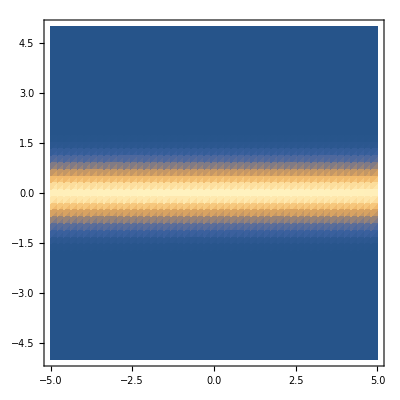

```mathematica
DensityPlot[Q3[Rz,Iz,4],{Rz,-5,5},{Iz,-5,5},PlotRange->Full,Mesh->False, PlotPoints->50,MaxRecursion->15]
```